# QuantumCircuit Usage Examples

Elementary usagepaclet:Q3/tutorial/QuantumCircuitUsage#1868432623 | Examples with Measurementspaclet:Q3/tutorial/QuantumCircuitUsage#1921589536
Grouping Circuit Elements With { }paclet:Q3/tutorial/QuantumCircuitUsage#188399535 | Examples with Controlled-Unitary Gatespaclet:Q3/tutorial/QuantumCircuitUsage#580366830
Automatic Conversion to Operator Expressionspaclet:Q3/tutorial/QuantumCircuitUsage#729173090 | Examples with Arbitrary Controlled-Unitary Gatespaclet:Q3/tutorial/QuantumCircuitUsage#87721419
More Complicated Gatespaclet:Q3/tutorial/QuantumCircuitUsage#2136908654 | Matrix on QuantumCircuitpaclet:Q3/tutorial/QuantumCircuitUsage#462801707
With Inputs and Outputspaclet:Q3/tutorial/QuantumCircuitUsage#94058740 | Matrix on QuantumCircuit: With Measurementpaclet:Q3/tutorial/QuantumCircuitUsage#991141748
Example with GraphStatespaclet:Q3/tutorial/QuantumCircuitUsage#175892259 |

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol provides the graphical representation of the quantum circuits.

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol | Graphical representation of quantum circuit
Phasepaclet:Q3/ref/PhaseQ3 Package Symbol | Single-qubit phase gate (relative phase)
Rotationpaclet:Q3/ref/RotationQ3 Package Symbol | Single-qubit rotation gate
EulerRotationpaclet:Q3/ref/EulerRotationQ3 Package Symbol | Single-qubit rotation gate specified by Euler angles
CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | Two-qubit controlled NOT gate
CZpaclet:Q3/ref/CZQ3 Package Symbol | Two-qubit controlled Z gate
Swappaclet:Q3/ref/SwapQ3 Package Symbol | Two-qubit Swap gate
Toffolipaclet:Q3/ref/ToffoliQ3 Package Symbol | Three-qubit Toffoli gate
ControlledGatepaclet:Q3/ref/ControlledGateQ3 Package Symbol | Multi-qubit controlled-U gate

Frequently used quantum circuit elements.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

## Elementary usage

First load the application (the collection of packages).

```mathematica
<<Q3`
```

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol works for labeled qubits.

```mathematica
Let[Qubit,S]
```

QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol is a collection of quantum logic gates. Usually, it is displayed in a graphical form.

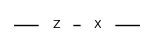

```mathematica
QuantumCircuit[S[1,3],S[1,1]]
```

Graphics directives can be used to change the style of labels of the quantum logic gates.

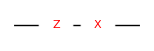

```mathematica
QuantumCircuit[Red,S[1,3],S[1,1]]
```

```mathematica
QuantumCircuit[Red,EdgeForm[Red],S[1,3],S[1,1]]
```

-Graphics-

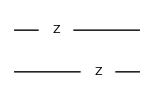

```mathematica
QuantumCircuit[Ket[],S[1,3],S[2,3]]
```

Here are all single-qubit gates displayed in a quantum circuit model.

```mathematica
QuantumCircuit[{S[1,1],S[2,2],S[3,3],S[4,6],S[5,7],S[6,8]},Null]
```

-Graphics-

“Spacer” is a special form to represent a time slice for no operation. It is useful for graphically extend certain time span. “Separator” puts a vertical dotted line to indicate a particular time slice.

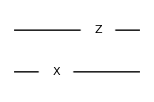

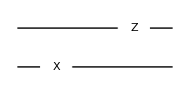

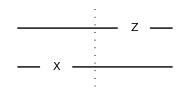

```mathematica
QuantumCircuit[S[2,1],S[1,3]]
QuantumCircuit[S[2,1],"Spacer",S[1,3]]
QuantumCircuit[S[2,1],"Separator",S[1,3]]
```

ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol or Elaboratepaclet:Q3/ref/ElaborateQ3 Package Symbol converts QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol to usual operator expressions in terms of the Pauli operators.

```mathematica
qc=QuantumCircuit[Blue, CNOT[S[1],S[2]]]
ExpressionFor[qc]
Elaborate[qc]
```

-Graphics-

1/2-1/2 S_(,,1)^(,,Z)S_(,,2)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,2)^(,,X)

1/2-1/2 S_(,,1)^(,,Z)S_(,,2)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,2)^(,,X)

Here is another example.

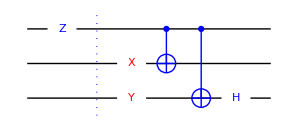

```mathematica
qc=QuantumCircuit[
Blue,S[1,3],"Separator",
{Red,EdgeForm[Red],S[2,1],S[3,2]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[3,6]]
```

```mathematica
op=S[3,6]**CNOT[S[1],S[3]]**CNOT[S[1],S[2]]**S[3,2]**S[2,1]**S[1,3]//Elaborate//Garner
```

-ⅈ/(2 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(2 √2)-(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,X))/(2 √2)+(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,Z))/(2 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X))/(2 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(2 √2)+(ⅈ S_(,,1)^(,,Z))/(2 √2)-(S_(,,3)^(,,Y))/(2 √2)

```mathematica
expr=ExpressionFor[qc]
```

-ⅈ/(2 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(2 √2)-(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,X))/(2 √2)+(ⅈ S_(,,2)^(,,X)S_(,,3)^(,,Z))/(2 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,X))/(2 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,3)^(,,Z))/(2 √2)+(ⅈ S_(,,1)^(,,Z))/(2 √2)-(S_(,,3)^(,,Y))/(2 √2)

```mathematica
op-expr//Garner
```

0

You can extend existing QuantumCircuit in a simple manner.

-Graphics-

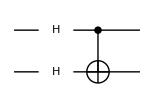

```mathematica
qc=QuantumCircuit[S[{1,2},6]]
QuantumCircuit[qc,CNOT[S[1],S[2]]]
```

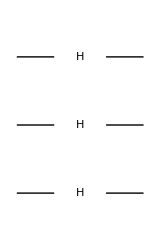

```mathematica
nn=Range[3];
qc=QuantumCircuit[Ket[S[nn]],S[nn,6],
ProductState[S[nn]->{1,1}],
"PortSize"->{0.65,2}]
```

```mathematica
expr=Elaborate[qc]
```

-Graphics-

You can give custom labels.

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))

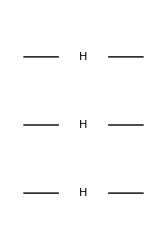

-Graphics-

```mathematica
in=Ket[S@nn]
qc=QuantumCircuit[{in,"Label"->"|m⟩"},S[nn,6],ProductState[S[nn]->{1,1}],
"PortSize"->{0.65,2}]
expr=Elaborate@qc
```

If the custom label is a list, then its elements are rotated.

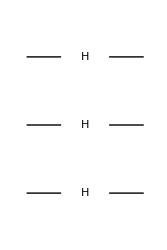

-Graphics-

```mathematica
qc=QuantumCircuit[
{Ket[S[nn]],"Label"->{"|m_0⟩","|m_1⟩"}},
S[nn,6],ProductState[S[nn]->{1,1}],
"PortSize"->{0.65,2}]
expr=Elaborate@qc
```

Controlled-unitary gates

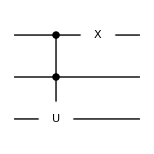

1/8 (2-√3) S_(,,1)^(,,X)S_(,,2)^(,,Z)-1/8 ⅈ S_(,,1)^(,,X)S_(,,3)^(,,Y)-1/8 ⅈ (-2+√3) S_(,,1)^(,,Y)S_(,,2)^(,,Z)+1/8 S_(,,1)^(,,Y)S_(,,3)^(,,Y)+1/8 ⅈ S_(,,1)^(,,X)S_(,,2)^(,,Z)S_(,,3)^(,,Y)-1/8 S_(,,1)^(,,Y)S_(,,2)^(,,Z)S_(,,3)^(,,Y)+1/8 (6+√3) S_(,,1)^(,,X)+1/8 ⅈ (-2+√3) S_(,,1)^(,,Y)

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (√3)/2 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | (√3)/2
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
qc=QuantumCircuit[
ControlledGate[S[{1,2}],Rotation[Pi/3,S[3,2],"Label"->"U"],"Label"->"R"],
S[1,1]]
expr=ExpressionFor[qc]
mat=Simplify@Matrix[qc];
MatrixForm[mat]
```

## Grouping Circuit Elements With { }

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

In QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol, Listpaclet:ref/List ({…}) can carry  two special meanings. First, it can put different quantum gates at the same time slice. Second, it can give options to particular quantum circuit elements.

### Putting different quantum logic gates at the same time slice.

Here all quantum logic gates are displayed at different time slices (along the horizontal direction).

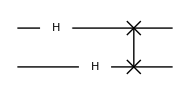

```mathematica
QuantumCircuit[S[1,6],S[2,6],Swap[S[1],S[2]]]
```

Here the first two gates are displayed at the same time slice while others are separated long the time (horizontal) direction.

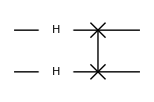

```mathematica
QuantumCircuit[{S[1,6],S[2,6]},Swap[S[1],S[2]]]
```

### Giving options to particular quantum logic gates or input/output states

This is one of the simplest cases.

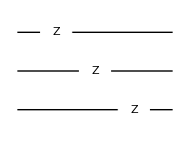

```mathematica
QuantumCircuit[S[1,3],S[2,3],S[3,3]]
```

In this example, the second and only the second gate is shown in red color.

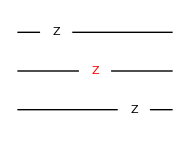

```mathematica
QuantumCircuit[S[1,3],{Red,S[2,3]},S[3,3]]
```

Unlike the example above, here all gates are displayed in red.

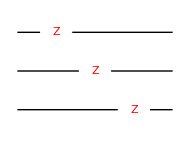

```mathematica
QuantumCircuit[Red,S[1,3],S[2,3],S[3,3]]
```

Here the second gate takes an option and it is labeled with “U” (not the default label “Z”).

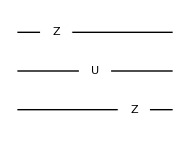

```mathematica
QuantumCircuit[S[1,3],{S[2,3],"Label"->"U"},S[3,3]]
```

## Automatic Conversion to Operator Expressions

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Consider an example of the entangler circuit model.

-Graphics-

-Graphics-

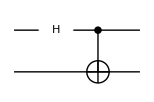

```mathematica
qc1=QuantumCircuit[S[1,6]]
qc2=QuantumCircuit[CNOT[S[1],S[2]]]
qc=QuantumCircuit[qc1,qc2]
```

This is the usual way to convert quantum circuit models into operator expressions.

```mathematica
op1=Elaborate[qc1]
op2=Elaborate[qc2]
op=Elaborate[qc]
```

(S_(,,1)^(,,X))/(√2)+(S_(,,1)^(,,Z))/(√2)

1/2-1/2 S_(,,1)^(,,Z)S_(,,2)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,2)^(,,X)

1/(2 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X))/(2 √2)-(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X))/(2 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X))/(2 √2)+(S_(,,1)^(,,X))/(2 √2)+(ⅈ S_(,,1)^(,,Y))/(2 √2)+(S_(,,1)^(,,Z))/(2 √2)-(S_(,,2)^(,,X))/(2 √2)

```mathematica
op-op2**op1
```

0

The above can also be achieve directly regarding the quantum circuit models as operators.

```mathematica
new=qc2**qc1 (* Notice the order. *)
```

1/(2 √2)+(S_(,,1)^(,,X)S_(,,2)^(,,X))/(2 √2)-(ⅈ S_(,,1)^(,,Y)S_(,,2)^(,,X))/(2 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,X))/(2 √2)+(S_(,,1)^(,,X))/(2 √2)+(ⅈ S_(,,1)^(,,Y))/(2 √2)+(S_(,,1)^(,,Z))/(2 √2)-(S_(,,2)^(,,X))/(2 √2)

```mathematica
op-new
```

0

## More Complicated Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

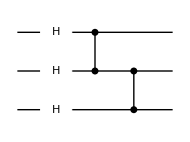

-Graphics-

```mathematica
qc=QuantumCircuit[S[{1,2,3},6],CZ[S[1],S[2]],CZ[S[2],S[3]]]
expr=ExpressionFor[qc]
EchoTiming[mat1=Matrix[qc];]
EchoTiming[mat2=Matrix[qc];]
mat2//MatrixForm
mat1-mat2//MatrixForm
```

0.001012

0.000921

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
-1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2)
-1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2) | -1/(2 √2)
1/(2 √2) | -1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | 1/(2 √2) | -1/(2 √2))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

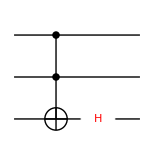

```mathematica
qc=QuantumCircuit[
Toffoli[S[1],S[2],S[3]],
Red,S[3,6]
]
```

```mathematica
op=Elaborate[qc]
expr=S[3,6]**Toffoli[S[1],S[2],S[3]]//Elaborate
op-expr//Garner
```

1/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z))/(4 √2)-(S_(,,2)^(,,Z))/(4 √2)+(3 S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,3)^(,,Y))/(4 √2)+(3 S_(,,3)^(,,Z))/(4 √2)

1/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z))/(4 √2)-(S_(,,2)^(,,Z))/(4 √2)+(3 S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,3)^(,,Y))/(4 √2)+(3 S_(,,3)^(,,Z))/(4 √2)

0

This is still another way to convert the quantum circuit to an operator expression.

```mathematica
ExpressionFor[qc]
```

1/(4 √2)+(S_(,,1)^(,,Z)S_(,,2)^(,,Z))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,1)^(,,Z)S_(,,3)^(,,Z))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)-(ⅈ S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)+(S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Y))/(4 √2)-(S_(,,1)^(,,Z)S_(,,2)^(,,Z)S_(,,3)^(,,Z))/(4 √2)-(S_(,,1)^(,,Z))/(4 √2)-(S_(,,2)^(,,Z))/(4 √2)+(3 S_(,,3)^(,,X))/(4 √2)+(ⅈ S_(,,3)^(,,Y))/(4 √2)+(3 S_(,,3)^(,,Z))/(4 √2)

## With Inputs and Outputs

You can specifies input and output states.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Real,a,b,c]
```

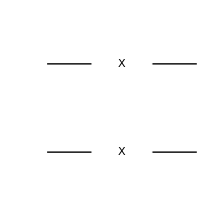

```mathematica
in=Ket[S[1]->0]+I Ket[S[1]->1];
qc=QuantumCircuit[
in,Ket[S@{2}],S[{1,2},1],
"PortSize"->2]
```

Specify the output manually, but it does not guarantee

```mathematica
out=Ket[]+I Ket[S[1]->1]+Ket[S[2]->1]//KetRegulate;
qc=QuantumCircuit[
in,Ket[S@{2,3}],S[{1,2,3},1],out,
"UnitLength"->42,
"PortSize"->3
]
```

-Graphics-

```mathematica
Clear[expr,mat];
expr[1]=S[2,1]+I S[4,3];
v1=Ket[S[2]->1]+ I Ket[S[3]->1];
mat[0]=ThePauli[{1,3}];
expr[2]=ExpressionFor[mat[0],S[{1,2}]];
qc=QuantumCircuit[v1,
ControlledGate[S[{3,4}],S[1,1]-S[2,2]],
ControlledGate[S[1],S[3,2]+I S[4,1]],
{expr[1],"Label"->"A"},
expr[1],{Ket[S[1]->1],v1}
]
```

-Graphics-

```mathematica
qc=QuantumCircuit[{expr[2],"Label"->"B"},
qc,Measurement[S[1,3]],S[3,6],
"PortSize"->2]
```

-Graphics-

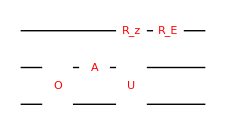

(ⅈ+(-1)^(5/6)) Cos[b/2] Cos[1/2 (a+c+ϕ)] S_(,,2)^(,,X)S_(,,4)^(,,Z)+1/2 (ⅈ+√3) Cos[1/2 (a-c-ϕ)] S_(,,1)^(,,Y)S_(,,2)^(,,Z) Sin[b/2]+(1+(-1)^(1/3)) Cos[1/2 (a-c-ϕ)] S_(,,1)^(,,Y)S_(,,2)^(,,X)S_(,,4)^(,,Z) Sin[b/2]-1/2 (ⅈ+√3) S_(,,1)^(,,X)S_(,,2)^(,,Z) Sin[b/2] Sin[1/2 (a-c-ϕ)]-(1+(-1)^(1/3)) S_(,,1)^(,,X)S_(,,2)^(,,X)S_(,,4)^(,,Z) Sin[b/2] Sin[1/2 (a-c-ϕ)]+1/2 Cos[b/2] S_(,,1)^(,,Z)S_(,,2)^(,,X)S_(,,4)^(,,Z) (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a+c)/2]+(3+ⅈ √3) Cos[(a+c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_(,,1)^(,,Z)S_(,,2)^(,,Z) (-2 (-ⅈ+(-1)^(5/6)) Cos[ϕ/2] Sin[(a+c)/2]+(ⅈ+√3) Cos[(a+c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_(,,2)^(,,Z) (2 (-1+(-1)^(1/3)) Cos[(a+c)/2] Cos[ϕ/2]+(1-ⅈ √3) Sin[(a+c)/2] Sin[ϕ/2])

(1/4 ⅈ (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | -1/4 (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | -1/4 (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | -1/4 ⅈ (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0
0 | 1/4 ⅈ (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | -1/4 (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 (3+ⅈ √3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b))
-1/4 (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (1-ⅈ √3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | -1/4 ⅈ (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0
0 | 1/4 (-3 ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (1-ⅈ √3) ⅇ^(-1/2 ⅈ (a+b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (3+ⅈ √3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 (ⅈ+√3) ⅇ^(-1/2 ⅈ (a+b-c-ϕ)) (-1+ⅇ^(ⅈ b))
1/4 (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 (3+ⅈ √3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 ⅈ (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | -1/4 (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0
0 | 1/4 (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | -1/4 ⅈ (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 ⅈ (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b))
1/4 (3+ⅈ √3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | -1/4 (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | -1/4 (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (1-ⅈ √3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0
0 | -1/4 ⅈ (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | -1/4 (ⅈ+√3) ⅇ^(1/2 ⅈ (a-b-c-ϕ)) (-1+ⅇ^(ⅈ b)) | 0 | 1/4 (-3 ⅈ+√3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)) | 0 | 1/4 (1-ⅈ √3) ⅇ^(1/2 ⅈ (a-b+c+ϕ)) (1+ⅇ^(ⅈ b)))

```mathematica
Let[Real,ϕ]
qc=QuantumCircuit[
Red,{expr[1],"Label"->"O"},
Phase[Pi/3,S[2,3],"Label"->"A"],
{Rotation[ϕ,S[1,3]],
{expr[1],"Label"->"U"}},
EulerRotation[{a,b,c},S[1]]
]
expr[0]=ExpressionFor[qc]
mat[0]=SimplifyThrough@Matrix[qc];
mat[0]//MatrixForm
```

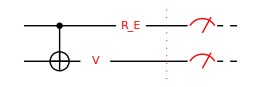

```mathematica
Let[Real,ϕ,a,b,c]
expr[1]=S[2,1]+I S[3,3];
qc=QuantumCircuit[
Ket[S[{1,2}]->1],
CNOT[S[1],S[2]],Red,
Rotation[ϕ,S[2,3],"Label"->"V"],
EulerRotation[{a,b,c},S[1]],
"Separator",
Measurement[S[{1,2},3]]
]
```

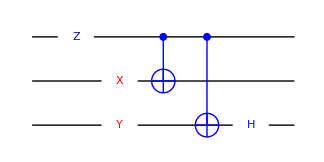

-6 ⅈ √2 0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))-42 ⅈ √2 0_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))-(9 ⅈ 0_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3)))/(√2)-(63 ⅈ 0_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3)))/(√2)+6 ⅈ √2 1_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))-42 ⅈ √2 1_(,,S_(,,1))0_(,,S_(,,2))1_(,,S_(,,3))+8 ⅈ √2 1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))-56 ⅈ √2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))

{-6 ⅈ √2,-42 ⅈ √2,(27 ⅈ)/(√2)-18 ⅈ √2,-(27 ⅈ)/(√2)-18 ⅈ √2,6 ⅈ √2,-42 ⅈ √2,8 ⅈ √2,-56 ⅈ √2}

```mathematica
qc=QuantumCircuit[
ProductState[S[{1,2,3}]->{3,4}],
Blue,S[1,3],
{Red,S[2,1],S[3,2]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],S[3,6],
"PortSize"->{2.5,0.5}
]
expr[0]=ExpressionFor[qc]
vec[0]=Matrix[qc]//Simplify;
vec[0]//Normal
```

## Example with GraphStates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Let us consider the graph states.



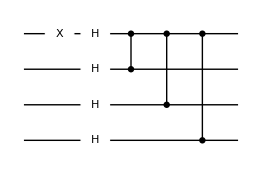

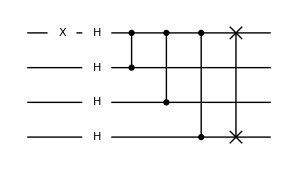

```mathematica
g=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
qc=QuantumCircuit[S[1,1],g]
qc=QuantumCircuit[qc,Swap[S[1],S[4]]]
```

```mathematica
EchoTiming[Elaborate[qc]]
```

2.94323

-Graphics-

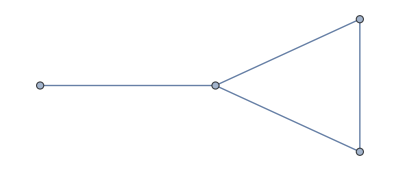

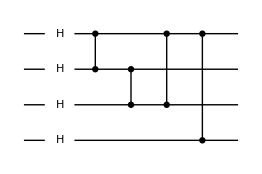

```mathematica
g=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]}]
QuantumCircuit[g]
```

```mathematica
qc=QuantumCircuit[Ket[S[{1,2,3,4}]],g]
```

-Graphics-

```mathematica
v[1]=Elaborate[qc]
v[2]=Matrix[qc];
v[2]//Normal
v[3]=GraphState[g]
v[1]-v[3]//Simplify//Normal
```

-Graphics-

{1/4,1/4,1/4,1/4,1/4,1/4,-1/4,-1/4,1/4,-1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4}

-Graphics-

0

## Examples with Measurements

Here are simple examples with measurements.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

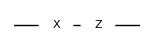

-1_(,,S_(,,1))

```mathematica
qc=QuantumCircuit[Ket[S@{1}],S[1,1],S[1,3]]
ex=ExpressionFor[qc]
```

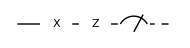

-1_(,,S_(,,1))

```mathematica
qc=QuantumCircuit[Ket[S@{1}],S[1,1],S[1,3],Measurement[S[1,3]]]
ex=ExpressionFor[qc]
```

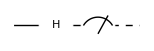

1_(,,S_(,,1))

```mathematica
qc=QuantumCircuit[Ket[S@{1}],S[1,6],Measurement[S[1,3]]]
ex=ExpressionFor[qc]
```

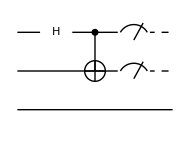

```mathematica
qc=QuantumCircuit[
Ket[S@{1,2,3}],
S[1,6],
CNOT[S[1],S[2]],
Measurement[S[{1,2},3]]
]
```

```mathematica
cc=ExpressionFor[qc]
```

0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))

Take another example

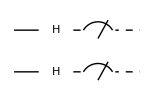

```mathematica
qc=QuantumCircuit[Ket[S@{1,2}],{S[1,6],S[2,6]},Measurement[S[{1,2},3]]]
```

```mathematica
data=Table[ExpressionFor[qc];Readout[S[{1,2},3]],{200}];
Histogram3D[data,AxesLabel->{S[1,$],S[2,$],"Counts"}]
```

-Graphics3D-

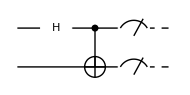

```mathematica
qc=QuantumCircuit[
Ket[S[{1,2}]->1],
S[1,6],CNOT[S[1],S[2]],
{Measurement[S[1,3]],Measurement[S[2,3]]}
]
```

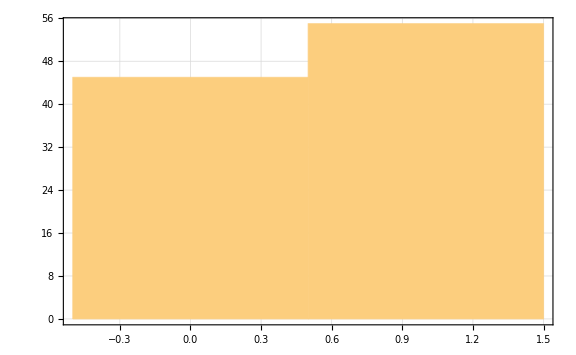

```mathematica
data=Table[ExpressionFor[qc];Readout[S[1,3]],{100}];
Histogram[data,Axes->False,Frame->True]
```

(0_(,,S_(,,1))1_(,,S_(,,2)))/(√2)-(1_(,,S_(,,1))0_(,,S_(,,2)))/(√2)

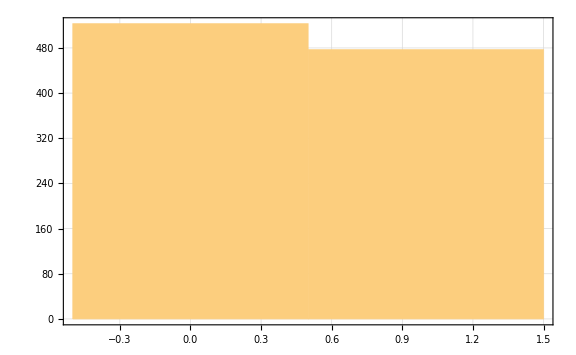

```mathematica
v=CNOT[S[1],S[2]]**S[1,6]**Ket[S[{1,2}]->1]
data=Table[
Measurement[S[1,3]]@Measurement[S[2,3]]@v;
Readout[S[1,3]],
{j,1000}
];
Histogram[data]
```

## Examples with Controlled-Unitary Gates

```mathematica
<<Q3`
```

Here are simple examples involving controlled-U gates.

```mathematica
Let[Qubit,S]
```

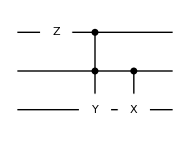

```mathematica
QuantumCircuit[
S[1,3],
ControlledGate[S[{1,2}],S[3,2]],
ControlledGate[S[2],S[3,1]]
]
```

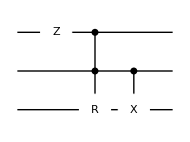

```mathematica
QuantumCircuit[
S[1,3],
ControlledGate[S[{1,2}],Rotation[Pi/3,S[3,2]],"Label"->"R"],
ControlledGate[S[2],S[3,1]]
]
```

## Examples with Arbitrary Controlled-Unitary Gates

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

S_(,,3)^(,,X)-ⅈ S_(,,3)^(,,Y)+1/2 S_(,,4)^(,,Z)

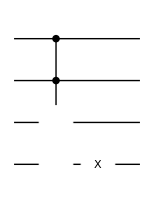

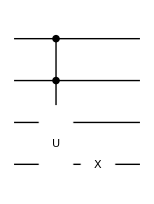

```mathematica
expr=S[3,1]- I S[3,2] + S[4,3]/2
qc1=QuantumCircuit[ControlledGate[S[{1,2}],expr],S[4,1]]
qc2=QuantumCircuit[ControlledGate[S[{1,2}],expr,"Label"->"U"],S[4,1]]
```

```mathematica
ex1=ExpressionFor[qc1]
ex2=ExpressionFor[qc2]
ex1-ex2//Simplify
```

-Graphics-

-Graphics-

0

Let us take another example, where the (multi-qubit) gate (operator) is expressed in an expression of Pauli operators for labelled qubits.

S_(,,3)^(,,0)+ⅈ S_(,,4)^(,,X)

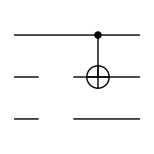

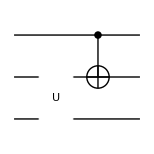

```mathematica
expr=S[3,0]+I S[4,1]
qc1=QuantumCircuit[ expr,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ {expr,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ExpressionFor[qc1]
ExpressionFor[qc2]
```

1/2-1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/2 ⅈ S_(,,1)^(,,Z)S_(,,4)^(,,X)+1/2 ⅈ S_(,,3)^(,,X)S_(,,4)^(,,X)-1/2 ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,X)S_(,,4)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,3)^(,,X)+1/2 ⅈ S_(,,4)^(,,X)

1/2-1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/2 ⅈ S_(,,1)^(,,Z)S_(,,4)^(,,X)+1/2 ⅈ S_(,,3)^(,,X)S_(,,4)^(,,X)-1/2 ⅈ S_(,,1)^(,,Z)S_(,,3)^(,,X)S_(,,4)^(,,X)+1/2 S_(,,1)^(,,Z)+1/2 S_(,,3)^(,,X)+1/2 ⅈ S_(,,4)^(,,X)

The gate is expressed in a matrix representation.

(ⅈ | 1
1 | -ⅈ)

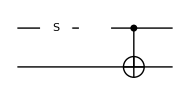

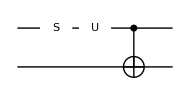

```mathematica
mat=ThePauli[1]+I ThePauli[3];
mat//MatrixForm
op=ExpressionFor[mat,S[1]];
qc1=QuantumCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ex1=Elaborate[qc1]
ex2=Elaborate[qc2]
ex1-ex2
```

ⅈ/2+1/2 S_(,,1)^(,,X)S_(,,3)^(,,X)-1/2 ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,X)-1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/2 ⅈ S_(,,1)^(,,X)-1/2 S_(,,1)^(,,Y)+1/2 ⅈ S_(,,1)^(,,Z)+1/2 S_(,,3)^(,,X)

ⅈ/2+1/2 S_(,,1)^(,,X)S_(,,3)^(,,X)-1/2 ⅈ S_(,,1)^(,,Y)S_(,,3)^(,,X)-1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)+1/2 ⅈ S_(,,1)^(,,X)-1/2 S_(,,1)^(,,Y)+1/2 ⅈ S_(,,1)^(,,Z)+1/2 S_(,,3)^(,,X)

0

Multi-qubit gate is expressed in a matrix representation.

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

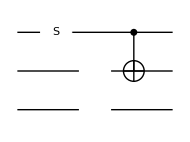

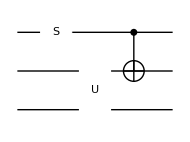

```mathematica
mat=ThePauli[{1,2}];
mat//MatrixForm
qq=S[{3,4}];
op=ExpressionFor[mat,qq];
qc1=QuantumCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc2=QuantumCircuit[ S[1,7],{op,"Label"->"U"},CNOT[S[1],S[3]]]
```

```mathematica
Elaborate[qc1]
Elaborate[qc2]
```

-1/2 ⅈ S_(,,1)^(,,Z)S_(,,4)^(,,Y)+1/2 S_(,,3)^(,,X)S_(,,4)^(,,Y)+1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)S_(,,4)^(,,Y)+1/2 ⅈ S_(,,4)^(,,Y)

-1/2 ⅈ S_(,,1)^(,,Z)S_(,,4)^(,,Y)+1/2 S_(,,3)^(,,X)S_(,,4)^(,,Y)+1/2 S_(,,1)^(,,Z)S_(,,3)^(,,X)S_(,,4)^(,,Y)+1/2 ⅈ S_(,,4)^(,,Y)

## Matrix on QuantumCircuit

Depending on the ratio of the “size” (the number of qubits) and the “depth” (the number of operations), Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol is more efficient than the ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

```mathematica
$n=4;
ss=S[Range[$n],$]
```

{S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=ControlledGate[S[j],S[k,C[k-j-1]],"Label"->Subscript["R",j-k]]/;j>k
CP[j_,k_]:=ControlledGate[S[j],S[k,C[j-k-1]],"Label"->Subscript["R",k-j]]/;j<k
SW[j_]:=Swap[S[j],S[$n-j+1]]
```

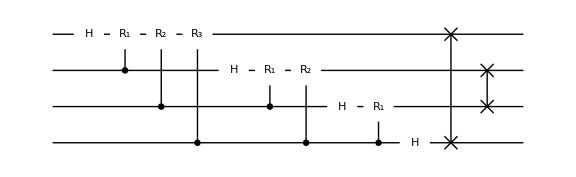

```mathematica
swaps=Table[SW[j],{j,1,$n/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$n},{j,k,$n}];
qft4a=Join[gates4a,swaps];
qc4a=QuantumCircuit[Sequence@@qft4a,ImageSize->Large]
```

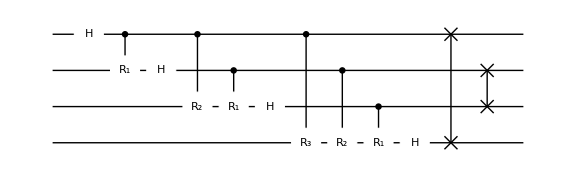

```mathematica
swaps=Table[SW[j],{j,1,$n/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$n},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuantumCircuit[Sequence@@qft4b,ImageSize->Large]
```

The above two circuits are actually equivalent.

```mathematica
EchoTiming[mat4a=Matrix[qc4a];]
EchoTiming[mat4b=Matrix[qc4b];]
mat4a-mat4b//N//Chop//Simplify//Normal//Flatten//DeleteCases[#,0]&
```

0.01348

0.009212

{}

## Matrix on QuantumCircuit: With Measurement

Here we illustrate how Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol works on a QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol when it involves Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

```mathematica
jj=Range[3];
ss=S[jj,$];
gg={Ket[ss->1]+I Ket[S[3]->1],
S[jj,6],
CNOT[S[1],S[2]],S[1,6],
CNOT[S[1],S[3]],
EulerRotation[{Pi/3,Pi/2,Pi/3},S[2]],
Measurement[S[2,3]],
S[1,3]};
qc=QuantumCircuit[Sequence@@gg,"PortSize"->{2,1}]
```

-Graphics-

```mathematica
mat1=Matrix[qc]//SimplifyThrough;
mat1//MatrixForm
mat2=Matrix[ExpressionFor@qc,ss];
mat2//MatrixForm
mat1-mat2//Simplify//Normal
{Readout[S[2,3]],Readout[S[2,3]]}
```

(((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3))
-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3))
0
0
0
0
0
0)

(((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3))
-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3))
0
0
0
0
0
0)

{0,0,0,0,0,0,0,0}

{0,0}

Let us collect the measurement readouts to get the statistics.

```mathematica
mp=Matrix[S[2,3],S@{1,2,3}];
EchoTiming[data1=Table[Matrix[qc];Readout[mp],100];]
Histogram[data1]
```

2.1309

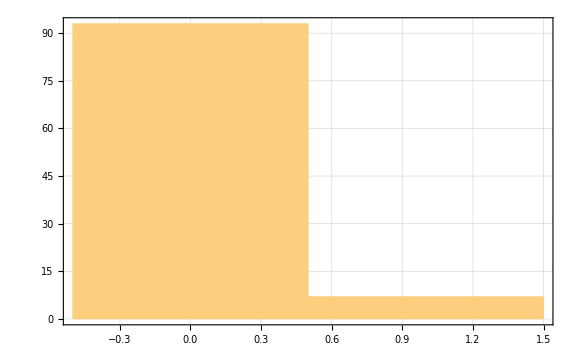

```mathematica
EchoTiming[data2=Table[ExpressionFor[qc];Readout[S[2,3]],100];]
Histogram[data2]
```

9.31678

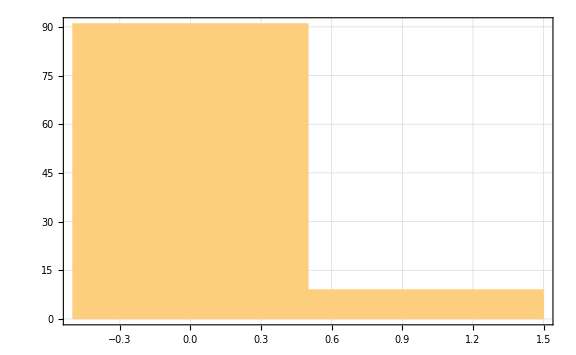

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Systems with Q3
▪Quantum Computation: Overview
▪Quantum Algorithms
▪Quantum Error-Correction Codes
▪Quantum Teleportation
▪Quantum Fourier Transform
▪Quantum Fourier Transform: Semiclassical Implementation

| Related Wolfram Education Group Courses
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/